# Gaussian Beam Propagation

```mathematica
Clear["Global`*"]
```

## Definitions

## Initialization

```mathematica
mm= 10^-3; um = 10^-6 ; mrad = 10^-3; urad = 10^-6; nm = 10^-9;
```

```mathematica
SetOptions[Plot, LabelStyle->{Black,14},PlotTheme->"Automatic",PlotRangePadding->None, Frame->True];
SetOptions[ListPlot, LabelStyle->{Black,14},PlotTheme->"Automatic",PlotRangePadding->None, Frame->True];
SetOptions[LogPlot, LabelStyle->{Black,14},PlotTheme->"Automatic",PlotRangePadding->None, Frame->True];
SetOptions[LogLogPlot, LabelStyle->{Black,14},PlotTheme->"Automatic",PlotRangePadding->None, Frame->True];
plotopt = { LabelStyle->{Black,14},PlotTheme->"Scientific",PlotRangePadding->None};
```

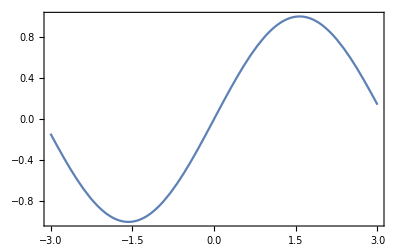

```mathematica
Plot[ Sin[x],{x,-3,3}]
```

```mathematica
SetOptions
```

SetOptions

Define real and imaginary for case when all variables are real. This gives better analytic results since usually Re[] and Im[] don’t simplify with FullSimplify, even with assumptions.

```mathematica
Conj[v_]:=v/.{Complex[x_,y_]-> Complex[x,-y]};
Re2[v_]:=  (v+Conj[v])/2; 
Im2[v_]:=   (v-Conj[v])/(2 ⅈ);
```

## Complex ABCD Matrix definitions

See my onenote on Complex ABCD Matrices.   The complex q parameter is related to the radius of curvature and waist by  1/q= 1/R-ⅈ λ_0/(π w^2).
Given an optical system represented by an ABCD matrix,  q_2= (A q_1+B)/(C q_1+D).

Define the ABCD definitions.

```mathematica
ClearAll[Lens,L,ROC,waist,qProp,λ,q0Define,w];
Lens[f_]:= ({{1, 0}, {-1/f, 1}})  ;   L[d_]:=  ({{1, d}, {0, 1}}); II = ({{1, 0}, {0, 1}});

(*Define the initial q*)
q0Define[ R_,w_,z0_: 0]:=  Module[{},(1/R- ⅈ λ/(π w^2))^-1-z0];  (*z0 is z positoin of the wiast, and is optional*)


ROC[q_?NumberQ]:= 1/Re[1/q]  ;  
waist[q_?NumberQ]:=  Module[{},   √((- λ)/(π Im[1/q])) ] ; 
  (*use for analytic solutions*)
ROC2[q_]:= 1/Re2[1/q]  ;  
waist2[q_]:=  Module[{},   √((- λ)/(π Im2[1/q])) ] ; 
(*Propagate the q using ABCD matrix, M*)
qProp[q1_?NumberQ, M_?ListQ]:=Module[{}, (M⟦1,1⟧ q1 + M⟦1,2⟧)/(M⟦2,1⟧ q1 + M⟦2,2⟧)] ;
```

#### Old Calculations

Look at the waist and ROC of a Gaussian beam (z=0 is w_0):

```mathematica
Clear[z,w,λ];
q0 = qDefine[∞,w];
M = L[z];
FullSimplify[  waist[  qProp[q0,M]] ]
FullSimplify[ R[  qProp[q0,M]] ]
```

waist[qProp[qDefine[∞,w],{{1,z},{0,1}}]]

R[qProp[qDefine[∞,w],{{1,z},{0,1}}]]

Now look at the waist after a lens, then propagation.

```mathematica
Clear[z,w,λ,f];
q0 = qDefine[∞,w];
M = L[z].Lens[f];
lenswaist= FullSimplify[  waist[  qProp[q0,M]] ]
FullSimplify[ R[  qProp[q0,M]] ]
```

waist[qProp[qDefine[∞,w],{{1-z/f,z},{-1/f,1}}]]

R[qProp[qDefine[∞,w],{{1-z/f,z},{-1/f,1}}]]

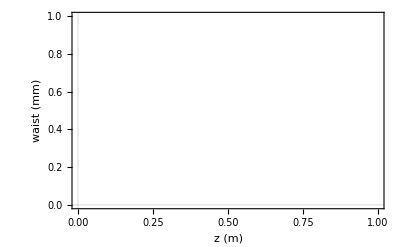

```mathematica
f = 1000 mm; 
w = 0.6 mm; 
λ = 0.8 um; 

Plot[ 1/mm  lenswaist,{z,0,2 f},PlotRange->{0,All},PlotTheme->"Scientific", FrameLabel->{"z (m)","waist (mm)"},LabelStyle->{Black,14}]
```

Now look at the waist after a lens, then propagation.

```mathematica
Clear[z,w,λ,f];
q0 = qDefine[∞,w];
M = L[z].Lens[f];
lenswaist= FullSimplify[  waist[  qProp[q0,M]] ]
FullSimplify[ R[  qProp[q0,M]] ]
```

waist[qProp[qDefine[∞,w],{{1-z/f,z},{-1/f,1}}]]

R[qProp[qDefine[∞,w],{{1-z/f,z},{-1/f,1}}]]

```mathematica
f = 2000 mm; 
w = 0.6 mm; 
λ = 0.8 um; 

Plot[ 1/mm  lenswaist,{z,0,2 f},PlotRange->{0,All},PlotTheme->"Scientific", FrameLabel->{"z (m)","waist (mm)"},LabelStyle->{Black,14}]
```

-Graphics-

Now I try a second lens with the same focal length

```mathematica
Clear[z,w,λ,f1,f2,z1];
q0 = qDefine[∞,w];
M =L[z].Lens[f2].L[z1].Lens[f1];
lenswaist= FullSimplify[  waist[  qProp[q0,M]] ]
(*FullSimplify[ R[  qProp[q0,M]] ]*)
```

waist[qProp[qDefine[∞,w],{{(f1 (f2-z)+z z1-f2 (z+z1))/(f1 f2),z+z1-(z z1)/f2},{-(f1+f2-z1)/(f1 f2),1-z1/f2}}]]

```mathematica
f1 = 2000 mm; 
f2=1500 mm;
w = 0.6 mm; 
λ = 0.8 um; 
z1=1.5 ;
(*Piecewise[{ {w1,z<f1},{w2,z>f1}}]*)
Plot[ lenswaist 1/mm,{z,0,2 f},PlotRange->{0,All},PlotTheme->"Scientific", FrameLabel->{"z (m)","waist (mm)"},LabelStyle->{Black,14}]
```

-Graphics-

```mathematica
Piecewise[{ {w1,z<f1},{w2,z>f1}}]
```

Piecewise[{{w1, z<2}, {w2, z>2}, {0, True}}]

Automate

```mathematica
Clear[z,w,λ,f,f2,z1,z2,q0,M,M1,M2,w1,w2,f1,w0];
q0 = qDefine[∞,w0];

M1 =L[z1].Lens[f1];
q1=qProp[q0, M1];
w1 = waist[q1];

M2 =L[z2].Lens[f2];
q2=qProp[q1, M2];
w2 = waist[q2];
```

```mathematica
w2
```

waist[qProp[qProp[qDefine[∞,w0],{{1-z1/f1,z1},{-1/f1,1}}],{{1-z2/f2,z2},{-1/f2,1}}]]

```mathematica
Clear[f1,f2,z1,z2];
w0=0.6 mm; λ = 0.8um;
f1 = 1000 mm; 
z1f = 1000 mm; 
f2 = 500 mm; 

plot1 = Plot[ 1/mm  w1,{z1,0,z1f},PlotRange->{0,All},PlotTheme->"Scientific", FrameLabel->{"z (m)","waist (mm)"},LabelStyle->{Black,14},PlotRangePadding->None];
plot2=Plot[ 1/mm  w2//.{z1->z1f,z2->z2p-z1f},{z2p,z1f,2},PlotRange->{0,All},PlotTheme->"Scientific", FrameLabel->{"z (m)","waist (mm)"},LabelStyle->{Black,14}];
Show[plot1,plot2,PlotRange->{{0,All},{0,All}}]
```

-Graphics-

```mathematica
Clear[f1,f2,z1,z2];
w0=0.6 mm; λ = 0.8um;
f1 =400 mm; 
f2 = 1.05f1; 
z1f =  800 mm; 
plot1 = Plot[ 1/mm  w1,{z1,0,z1f},PlotRange->{0,All},PlotTheme->"Scientific", FrameLabel->{"z (m)","waist (mm)"},LabelStyle->{Black,14},PlotRangePadding->None];
plot2=Plot[ 1/mm  w2//.{z1->z1f,z2->z2p-z1f},{z2p,z1f,2},PlotRange->{0,All},PlotTheme->"Scientific", FrameLabel->{"z (m)","waist (mm)"},LabelStyle->{Black,14}];
Show[plot1,plot2,PlotRange->{{0,All},{0,All}}]
```

-Graphics-

```mathematica
w0 =0.6 mm
zR = π w0^2/λ
```

0.0006

1.41372

```mathematica
6.4*10^-3 360/(2 π)
```

0.366693

```mathematica
Mag = 6.7;
1/um 6.4 mrad 18mm  1/Mag
```

17.194

## Multi-element propagation

The goal is to create a function that produces the ABCD matrix for any position of a multi-lens system.

```mathematica
Clear[OpticalElementsFolded,OpticalElementPW,LengthsFolded];
OpticalElementPW[OpticalElements_,z_]:=Module[{lengths},
lengths = OpticalElements⟦All,2⟧;
FoldList[ (#1⟦1⟧+#2 > z≥ #1⟦1⟧)&   , lengths⟦1⟧>z≥ 0,  Rest@lengths]
];

OpticalElementsFolded[OpticalElements_,z_]:=Module[{OE,folded},
OE =OpticalElements;
OE⟦All,2⟧= RotateLeft[OE⟦All,2⟧,-1];
OE⟦1,2⟧=0;
folded=Rest@FoldList[#2⟦1⟧ .L[#2⟦2⟧].#1& , II,OE ]   ;

{folded, OpticalElementPW[OpticalElements,z]}ᵀ
];

LengthsFolded[OpticalElements_,z_]:=Module[{OE,folded,lengths},
lengths =Drop[Join[{0}, OpticalElements⟦All,2⟧],-1];
{Accumulate[lengths],OpticalElementPW[OpticalElements,z]}ᵀ
]
```

Testing the functions

```mathematica
Clear[f1,L1,f2,L2,z,L3,f3];
OpticalElements = {{Lens[f1],L1},{Lens[f2],L2},{Lens[f3],L3}};

OpticalElementPW[OpticalElements,z];
OEpw=OpticalElementsFolded[OpticalElements,z];
Piecewise@OEpw

LengthsFolded[OpticalElements,z]
```

Piecewise[{{{{1,0},{-1/f1,1}}, L1>z≥0}, {{{1-L1/f1,L1},{-1/f2-(1-L1/f2)/f1,1-L1/f2}}, L1+L2>z≥L1}, {{{1-L1/f1+(-1/f2-(1-L1/f2)/f1) L2,L1+(1-L1/f2) L2},{-(1-L1/f1)/f3+(-1/f2-(1-L1/f2)/f1) (1-L2/f3),-L1/f3+(1-L1/f2) (1-L2/f3)}}, L1+L2+L3>z≥L1+L2}, {0, True}}]

{{0,L1>z≥0},{L1,L1+L2>z≥L1},{L1+L2,L1+L2+L3>z≥L1+L2}}

Check that it gives me the expected elements

```mathematica
OEpw⟦1⟧⟦1⟧- Lens[f1]

OEpw⟦2⟧⟦1⟧  -  Lens[f2].L[L1].Lens[f1]  //Simplify

OEpw⟦3⟧⟦1⟧-  Lens[f3].L[L2].Lens[f2].L[L1].Lens[f1]  //Simplify
```

{{0,0},{0,0}}

{{0,0},{0,0}}

{{0,0},{0,0}}

Now I test the length function.

```mathematica
Lengths=OpticalElements⟦All,2⟧;
lengthspw = LengthsFolded[Lengths,z];
Piecewise[lengthspw]
```

Piecewise[lengthspw]

Now I create the function that produces the ABCD matrix for any position z in the system.

```mathematica
ClearAll[ABCDMatrix];
ABCDMatrix[z_?NumberQ,{Mfun_,pwfun_}]:=Module[{M,Δz},
M =Mfun[z];
Δz =( z- pwfun[z]);
 L[Δz].M
]
```

```mathematica
Clear[GetABCDMatrixBetweenTwoPoints,z1,z2];
GetABCDMatrixBetweenTwoPoints[z1_?NumberQ, z2_?NumberQ, {Mfun_,pwfun_}]:= Module[{M1,M2,M},
(*if z1=0, then I set M1 = Identity so that it does not include the first lens.  Therefore  GetABCDMatrixBetweenTwoPoints[z1=0,z2] includes the first lens, whereas before it didn't. *)
If[z1==0,
M1= II,
M1 = ABCDMatrix[z1,{Mfun,pwfun}]];

M2 = ABCDMatrix[z2,{Mfun,pwfun}];
M = M2.Inverse[M1]
]
```

```mathematica
?
```

Now I test with real numbers.  I also show that GetABCDMatrixBetweenTwoPoints works.

```mathematica
Clear[z,f1,L1,f2,L2,L3,f3];
f1=1;f2=2;f3=3;L1=1;L2=1;L3=1;
OpticalElements = {{Lens[f1],L1},{Lens[f2],L2},{Lens[f3],L3}};

(*Generate the functions for tbe sytem*)
Mfun[z_]=Piecewise@OpticalElementsFolded[OpticalElements,z];
pwfun[z_]=Piecewise@LengthsFolded[OpticalElements,z];

ABCDMatrix[1.2,{Mfun,pwfun}]

GetABCDMatrixBetweenTwoPoints[.999999,2.00000001, {Mfun,pwfun}]
```

{{-0.2,1.1},{-1.,0.5}}

{{0.5,1.},{-0.666667,0.666666}}

```mathematica
Clear[z,f1,L1,f2,L2,L3,f3];
f2=2;f3=3;L2=1;L3=.00001;
f1 = 10^6; L1 = 10^-6; 
OpticalElements = {{Lens[f1],L1},{Lens[f2],L2},{Lens[f3],L3}};
Mfun[z_]=Piecewise@OpticalElementsFolded[OpticalElements,z];
pwfun[z_]=Piecewise@LengthsFolded[OpticalElements,z];
ABCDMatrix[L1+L2+L3-10^-3,{Mfun,pwfun}]
```

{{0.500494,0.999011},{-0.500001,1.}}

```mathematica
Clear[z,OEFuntions];
OEFuntions[OpticalElements_]:=Module[{Mfun,pwfun},
Mfun[z_]=Piecewise@OpticalElementsFolded[OpticalElements,z]//N;
pwfun[z_]=Piecewise@LengthsFolded[OpticalElements,z]//N;
{Mfun,pwfun}
]
```

These are just functions so that I don’t have to remember ABCDMatrix and qProp.

```mathematica
WaistFun[q0_,OEfun_,z_]:=Module[{},waist[qProp[q0,ABCDMatrix[z,OEfun]]]];
ROCFun[q0_,OEfun_,z_]:=Module[{},ROC[qProp[q0,ABCDMatrix[z,OEfun]]]];
```

### Examples

```mathematica
Piecewise@OpticalElementsFolded[OpticalElements,z]//N
```

Piecewise[{{{{1.,0.},{-1.×10^-6,1.}}, 1.×10^-6>z≥0.}, {{{1.,1.×10^-6},{-0.500001,1.}}, 1.>z≥1.×10^-6}, {{{0.499999,1.},{-0.666667,0.666666}}, 1.00001>z≥1.}, {0., True}}]

```mathematica
Piecewise@LengthsFolded[OpticalElements,z]//N
```

Piecewise[{{0., 1.×10^-6>z≥0.}, {1.×10^-6, 1.>z≥1.×10^-6}, {1., 1.00001>z≥1.}, {0., True}}]

Next I plot the waist and ROC

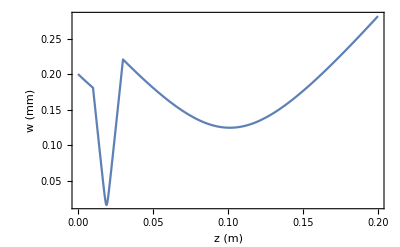

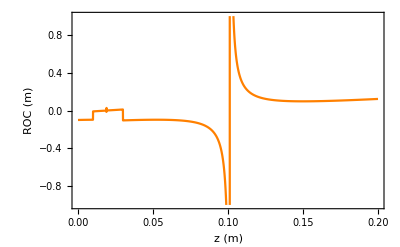

```mathematica
Clear[z,f1,L1,f2,L2,L3,f3,w0,R0,M,q0,z,Mfun,pwfun];
f1=100mm;L1=10mm;f2=10mm;L2=20mm;f3=10 mm;L3=10^6 mm;
R0=10^6;w0=0.2mm;
λ=1 um;
OpticalElements = {{Lens[f1],L1},{Lens[f2],L2},{Lens[f3],L3}};



(*Generate the functions for tbe sytem*)
q0=q0Define[R0,w0]//N;
Clear[z];

(*Mfun[z_]=Piecewise@OpticalElementsFolded[OpticalElements,z]//N;
pwfun[z_]=Piecewise@LengthsFolded[OpticalElements,z]//N;
waist@qProp[q0,ABCDMatrix[.02,{Mfun,pwfun}]]
Plot[1/mm waist@qProp[q0,ABCDMatrix[z,{Mfun,pwfun}]]  ,{z,0,.2},PlotRange->{0,All},PlotTheme->"Scientific"]
*)

(*OEfun=OEFuntions[OpticalElements];
Plot[1/mm waist@qProp[q0,ABCDMatrix[z,OEfun]]  ,{z,0,.2},PlotRange->{0,All},PlotTheme->"Scientific"]
*)

OEfun=OEFuntions[OpticalElements];
Plot[1/mm WaistFun[q0,OEfun,z]  ,{z,0,.2},PlotRange->{0,All},FrameLabel->{"z (m)","w (mm)"}]
Plot[ ROCFun[q0,OEfun,z]  ,{z,0,.2},PlotRange->{-1,1},PlotStyle->Orange,FrameLabel->{"z (m)","ROC (m)"}]
```

Next I find the minimum waist location.

```mathematica
FindMinimum[{1/mm WaistFun[q0,OEfun,z],z>0} ,{z,.2}]
```

{0.124535,{z→0.101227}}

```mathematica
GetABCDMatrixBetweenTwoPoints[0,0.1, OEfun]
```

{{-0.4,-0.06},{10.,-1.}}

```mathematica
ClearAll[DrawOpticalSystem,PlotLog,PlotROC];
Options[DrawOpticalSystem]=Join[ {PlotLog->"False",PlotROC->"False"},Options[Plot] ];
DrawOpticalSystem[OpticalElements_, {R0_,w0_,z0_}, opts:OptionsPattern[]]:=Module[{LensPositions,q0,OEfun,plot1,PlotFun,ylabel,Plotf},
(*plots*)
LensPositions =Join[{0},Accumulate[OpticalElements⟦All,2⟧]];
q0=q0Define[R0,w0,z0]//N;
Clear[z];
OEfun=OEFuntions[OpticalElements];

(*Options*)
If[OptionValue[PlotROC]=="True",
PlotFun=Abs[10^-3 ROCFun[#1,#2,#3]]&; ylabel="|R|(m)";,
PlotFun = WaistFun; ylabel="w (mm)"];
If[OptionValue[PlotLog]=="True",
Plotf=LogPlot,
Plotf = Plot];

(*plot*)
plot1= Plotf[1/mm PlotFun[q0,OEfun,z]  ,{z,0,Last@LensPositions},FrameLabel->{"z (m)",ylabel},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],Evaluate@FilterRules[{opts},Options[Plot]]];

{{q0,OEfun,LensPositions},plot1}

]
```

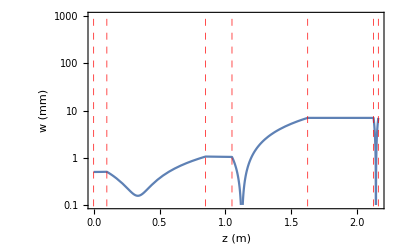

```mathematica
Clear[z,f1,L1,f2,L2,L3,f3,w0,R0,M,q0,z,OEfun];
(*Define simulation*)
f0=10^6; L0 = 100mm; (*initial*)
fa= 250 mm;  La = 750mm; fb = 500mm; Lb =200mm;  (*relay*)
f1=75mm;f2=500mm;L1=(575)mm;L2=500mm; (*telescope*)
fobj=18mm;Lobj=2*fobj; (*objective*)
R0=10^6;w0=0.5mm;z0=0; (*initial waist*)
λ=1 um;
OpticalElements = {{Lens[f0],L0},{Lens[f1],L1},{Lens[f2],L2},{Lens[fobj],Lobj}}//N;
OpticalElements = {{Lens[f0],L0},{Lens[fa],La},{Lens[fb],Lb},{Lens[f1],L1},{Lens[f2],L2},{Lens[fobj],Lobj}}//N;


{{q0,OEfun,LensPositions},plot}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{.1,1000},PlotROC->"False"];
plot
```

```mathematica
ClearAll[DisplacementAODProperties];
DisplacementAODProperties[zAOD_?NumberQ,zmin_?NumberQ,OEfun_,θtrap_]:=Module[{Mtweezer,Δxtrap,θMag},
Mtweezer = GetABCDMatrixBetweenTwoPoints[zAOD,zmin, OEfun];
(*Mtweezer//MatrixForm ;*)
Δxtrap=1/um θtrap Mtweezer⟦1,2⟧/Mtweezer⟦2,2⟧  ;(*displacement of trap for rotation θtrap (um) *)
θMag = Mtweezer⟦2,2⟧;
{Δxtrap,θMag}
]
```

wmin (um) | 0.820787
z from last lens (mm)  | 17.9993

{0.000816934,192.137}

Trap Displacement for 20 mrad rotation (nm):  | Δxtrap
AOD Angle magnification:  | θMag

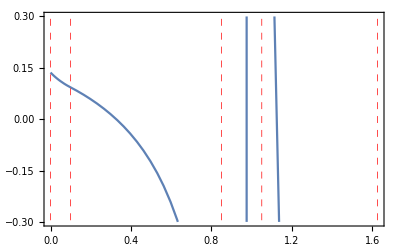

```mathematica
min = FindMinimum[{ WaistFun[q0,OEfun,z],LensPositions⟦-1⟧>z>LensPositions⟦-2⟧} ,{z,Mean@LensPositions⟦{-1,-2}⟧}];
wmin= min⟦1⟧;  zmin =( z/.min⟦2⟧ ) ;

Grid@{{"wmin (um)",wmin /um},{
"z from last lens (mm) ",(zmin-LensPositions⟦-2⟧)/mm}}

zAOD = L0+fa -25mm; 
DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]

Grid@{{"Trap Displacement for 20 mrad rotation (nm): ",Δxtrap},{
"AOD Angle magnification: ",θMag }}

Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦1⟧  ,{zAOD,0,LensPositions⟦-3⟧},PlotRange->{-0.3,0.3},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed]]
```

## Calculations

## Collimated before tweezer telescope

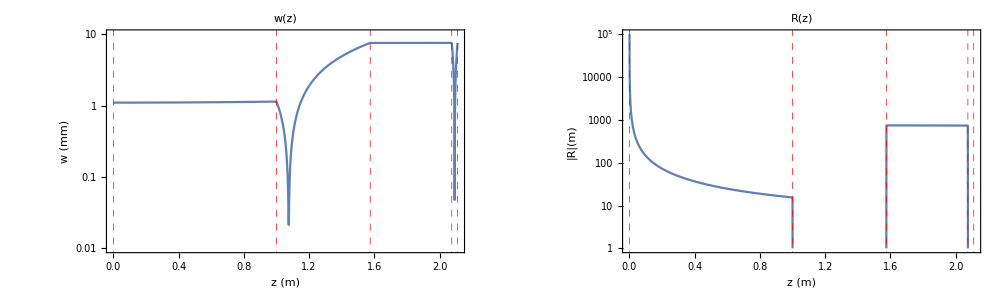

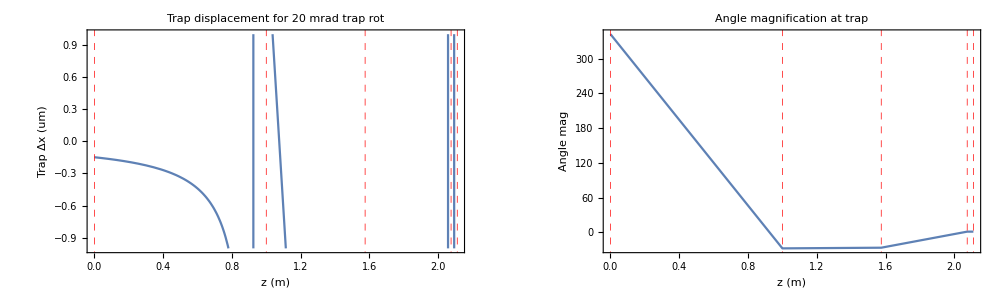

wmin (um) | 0.759176
z from focus (um)  | 0.434769
zmin (m) | 2.093

```mathematica
Clear[z,f1,L1,f2,L2,L3,f3,w0,R0,M,q0,z,OEfun];
(*Define simulation*)
f0=10^6; L0 = 1000mm; (*initial*)
(*fa= 10^6 mm;  La = 10^-6 mm; fb = 10^6 mm; Lb =1mm;  (*relay*)*)
f1=75mm;f2=500mm;L1=(575)mm;L2=500mm; (*telescope*)
fobj=18mm;Lobj=2*fobj; (*objective*)
R0=10^6;w0=1.1mm;z0=0; (*initial waist*)
λ=1 um;
OpticalElements = {{Lens[f0],L0}(*,{Lens[fa],La},{Lens[fb],Lb}*),{Lens[f1],L1},{Lens[f2],L2},{Lens[fobj],Lobj}}//N;


(*Plot w and R of optical system*)
{{q0,OEfun,LensPositions},plotw}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{.01,10},PlotROC->"False",PlotLabel->"w(z)"];
{{q0,OEfun,LensPositions},plotR}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{1,100000},PlotROC->"True",PlotLabel->"R(z)"];
GraphicsGrid[{{plotw,plotR}},ImageSize->1000]

(*Find the trap z position*)
min = FindMinimum[{ WaistFun[q0,OEfun,z],LensPositions⟦-1⟧>z>LensPositions⟦-2⟧} ,{z,Mean@LensPositions⟦{-1,-2}⟧}];
wmin= min⟦1⟧;  zmin =( z/.min⟦2⟧ ) ;

(*Plot trap rotation and displacement vs z position of AOD*)
plotΔx=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦1⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{-1,1},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Trap Δx (um) "},PlotLabel->"Trap displacement for 20 mrad trap rot"];
plotMag=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦2⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{All,All},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Angle mag "},PlotLabel->"Angle magnification at trap"];
GraphicsGrid[{{plotΔx,plotMag}},ImageSize->1000]

Grid@{{"wmin (um)",wmin /um},{
"z from focus (um) ",(zmin-LensPositions⟦-2⟧-fobj)/um},{"zmin (m)",zmin}}
```

I try to simplify the ABCD matrix for the telescope.   So that I can get an analytic solution later.

```mathematica
Lens[g2].L[g1+g2].Lens[g1]  //FullSimplify
```

{{-g2/g1,g1+g2},{0,-g1/g2}}

```mathematica
L[g2].Lens[g2].L[g1+g2].Lens[g1]  //FullSimplify
```

{{-g2/g1,g2},{0,-g1/g2}}

```mathematica
L[g2].Lens[g2].L[g1+g2].Lens[g1].L[g1]  //FullSimplify
```

{{-g2/g1,0},{0,-g1/g2}}

```mathematica
L[Δz].L[gobj].Lens[gobj].L[g2].Lens[g2].L[g1+g2].Lens[g1].L[g1].L[d]  //FullSimplify
```

{{(g2 Δz)/(g1 gobj),(d g2^2 Δz-g1^2 gobj (gobj+Δz))/(g1 g2 gobj)},{g2/(g1 gobj),-g1/g2+(d g2)/(g1 gobj)}}

## Displacement telescope 1:1

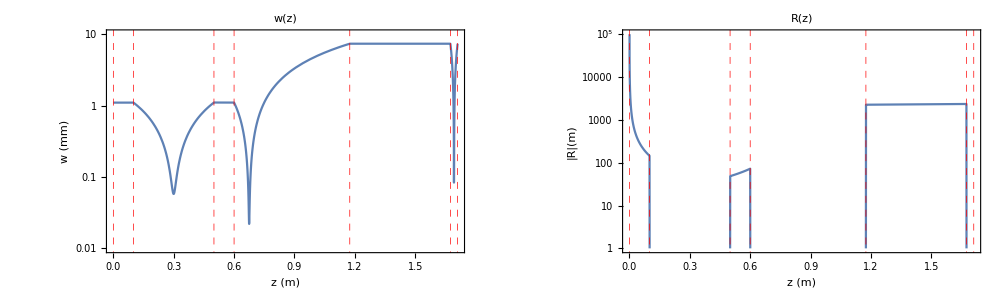

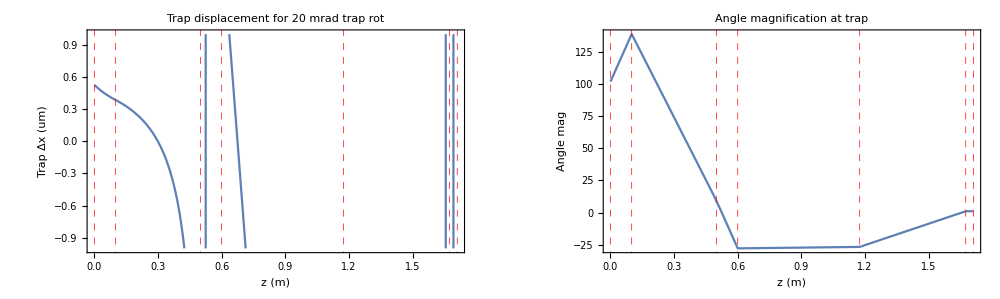

wmin (um) | 0.779264
z from focus (um)  | -0.140559
zmin (m) | 1.693

```mathematica
Clear[z,f1,L1,f2,L2,L3,f3,w0,R0,M,q0,z,OEfun];
(*Define simulation*)
f0=10^6; L0 = 100mm; (*initial*)
fa= 200 mm; fb = 200 mm; La = 400mm;  Lb =100mm;  (*relay*)
f1=75mm;f2=500mm;L1=(575)mm;L2=500mm; (*telescope*)
fobj=18mm;Lobj=2*fobj; (*objective*)
R0=10^6;w0=1.1mm;z0=0; (*initial waist*)
λ=1 um;
OpticalElements = {{Lens[f0],L0},{Lens[fa],La},{Lens[fb],Lb},{Lens[f1],L1},{Lens[f2],L2},{Lens[fobj],Lobj}}//N;


(*Plot w and R of optical system*)
{{q0,OEfun,LensPositions},plotw}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{.01,10},PlotROC->"False",PlotLabel->"w(z)"];
{{q0,OEfun,LensPositions},plotR}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{1,100000},PlotROC->"True",PlotLabel->"R(z)"];
GraphicsGrid[{{plotw,plotR}},ImageSize->1000]

(*Find the trap z position*)
min = FindMinimum[{ WaistFun[q0,OEfun,z],LensPositions⟦-1⟧>z>LensPositions⟦-2⟧} ,{z,Mean@LensPositions⟦{-1,-2}⟧}];
wmin= min⟦1⟧;  zmin =( z/.min⟦2⟧ ) ;

(*Plot trap rotation and displacement vs z position of AOD*)
plotΔx=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦1⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{-1,1},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Trap Δx (um) "},PlotLabel->"Trap displacement for 20 mrad trap rot"];
plotMag=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦2⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{All,All},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Angle mag "},PlotLabel->"Angle magnification at trap"];
GraphicsGrid[{{plotΔx,plotMag}},ImageSize->1000]

Grid@{{"wmin (um)",wmin /um},{
"z from focus (um) ",(zmin-LensPositions⟦-2⟧-fobj)/um},{"zmin (m)",zmin}}
```

## Displacement telescope 1:1 v2

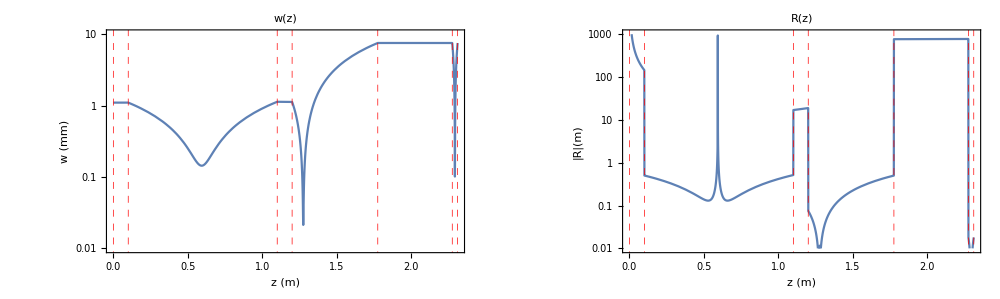

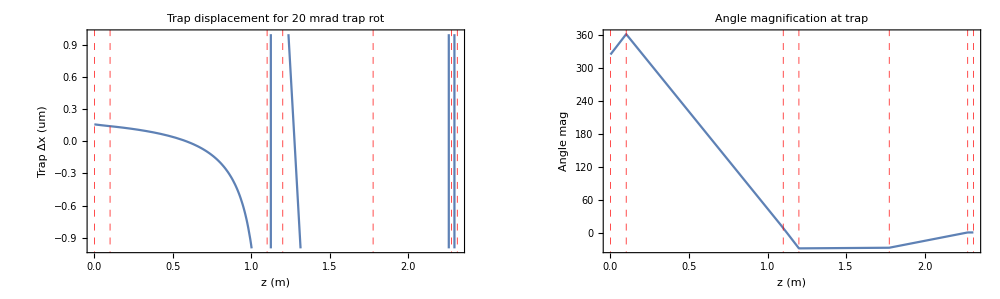

wmin (um) | 0.761381
z from focus (um)  | -0.425
zmin (m) | 2.293

```mathematica
Clear[z,f1,L1,f2,L2,L3,f3,w0,R0,M,q0,z,OEfun];
(*Define simulation*)
f0=10^6; L0 = 100 mm; (*initial*)
fa= 500mm; fb =500mm; La = 1000mm;  Lb =100mm;  (*relay*)
f1=75mm;f2=500mm;L1=(575)mm;L2=500mm; (*telescope*)
fobj=18mm;Lobj=2*fobj; (*objective*)
R0=10^6;w0=1.1mm;z0=0; (*initial waist*)
λ=1 um;
OpticalElements = {{Lens[f0],L0},{Lens[fa],La},{Lens[fb],Lb},{Lens[f1],L1},{Lens[f2],L2},{Lens[fobj],Lobj}}//N;


(*Plot w and R of optical system*)
{{q0,OEfun,LensPositions},plotw}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{.01,10},PlotROC->"False",PlotLabel->"w(z)"];
{{q0,OEfun,LensPositions},plotR}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{.01,1000},PlotROC->"True",PlotLabel->"R(z)"];
GraphicsGrid[{{plotw,plotR}},ImageSize->1000]

(*Find the trap z position*)
min = FindMinimum[{ WaistFun[q0,OEfun,z],LensPositions⟦-1⟧>z>LensPositions⟦-2⟧} ,{z,Mean@LensPositions⟦{-1,-2}⟧}];
wmin= min⟦1⟧;  zmin =( z/.min⟦2⟧ ) ;

(*Plot trap rotation and displacement vs z position of AOD*)
plotΔx=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦1⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{-1,1},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Trap Δx (um) "},PlotLabel->"Trap displacement for 20 mrad trap rot"];
plotMag=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦2⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{All,All},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Angle mag "},PlotLabel->"Angle magnification at trap"];
GraphicsGrid[{{plotΔx,plotMag}},ImageSize->1000]

Grid@{{"wmin (um)",wmin /um},{
"z from focus (um) ",(zmin-LensPositions⟦-2⟧-fobj)/um},{"zmin (m)",zmin}}
```

```mathematica
.
```

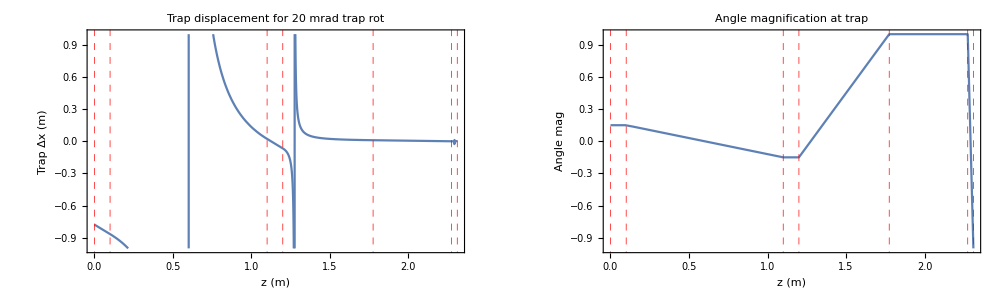

```mathematica
zmin=LensPositions⟦-2⟧-10^-9; (*set z at objective lens*)
plotΔx=Plot[ 10^-6 DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦1⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{-1,1},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Trap Δx (m) "},PlotLabel->"Trap displacement for 20 mrad trap rot"];
plotMag=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦2⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{All,All},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Angle mag "},PlotLabel->"Angle magnification at trap"];
GraphicsGrid[{{plotΔx,plotMag}},ImageSize->1000]
```

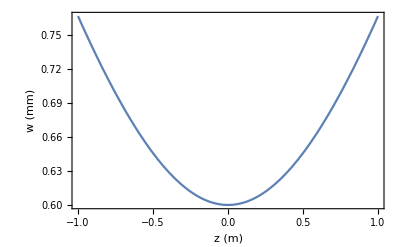

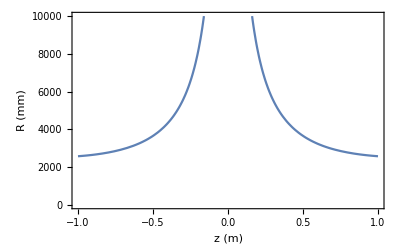

```mathematica
wo = 600um; λ = 0.9um;
zR = π wo^2/λ  ; 
RGauss[z_]:=z (1+ (zR/z)^2);
wGauss[z_]:= wo √(1+(z/zR)^2); 
range=1;
Plot[ 1/mm wGauss[z] ,{z,-range,range},FrameLabel->{"z (m)","w (mm)"},PlotRange->{0,All}]
Plot[ Abs[1/mm RGauss[z]] ,{z,-range,range},FrameLabel->{"z (m)","R (mm)"},PlotRange->{0,10000}]
```

## 700nm with weak lens inside telescope fd,f1,f2 fd, f2 = telescope lenses f1 = weak lens fobj=1m “diagnosis” lens put in f1 = 10^6 to see nominal waist size and location nominal location: 1976.2 for 16.2mm fobj

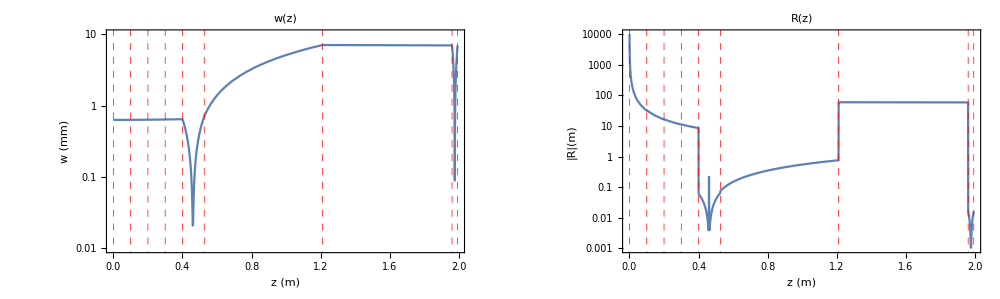

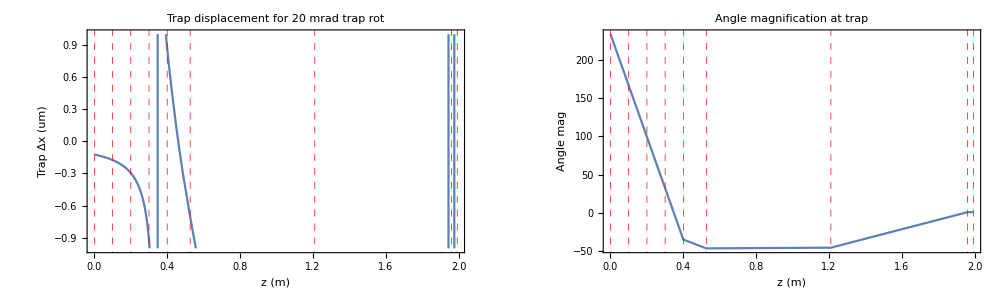

wmin (um) | 0.518354
z from focus (um)  | -4.46078
zmin (m) | 1.9762

```mathematica
(*Define simulation*)

R0=10^6;w0=.63 mm;z0=0; (*initial waist*)
λ=700nm;
z00=1976.2mm;
f0=10^6; L0 = 100mm; (*initial*)
fd = 60 mm; (*first telescope lens*)
f1=.5;(*cylindrical lens*)
f2=750mm;(*second telescope lens*)
fobj=16.2mm;
traplocs=Reap[Do[
fa= 10^6 mm; fb =  10^6 mm; La = 100mm;  Lb =100mm;  (*relay*)
fc = 10^6 mm;Lc = 100mm;L1=fd+f2-Ld;L2=f2; (*telescope*)
Lobj=2*fobj; (*objective*)

OpticalElements = {{Lens[f0],L0},{Lens[fa],La},{Lens[fb],Lb},{Lens[fc],Lc},{Lens[fd],Ld},{Lens[f1],L1},{Lens[f2],L2},{Lens[fobj],Lobj}}//N;

(*Plot w and R of optical system*)
{{q0,OEfun,LensPositions},plotw}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{.01,10},PlotROC->"False",PlotLabel->"w(z)"];
{{q0,OEfun,LensPositions},plotR}=DrawOpticalSystem[OpticalElements,{R0,w0,z0},PlotLog->"True",PlotRange->{.001,10000},PlotROC->"True",PlotLabel->"R(z)"];


(*Find the trap z position*)
min = FindMinimum[{ WaistFun[q0,OEfun,z],LensPositions⟦-1⟧>z>LensPositions⟦-2⟧} ,{z,Mean@LensPositions⟦{-1,-2}⟧}];
wmin= min⟦1⟧;  zmin =( z/.min⟦2⟧ ) ;
Sow[{Ld,(zmin-z00)/mm,wmin/um}],
{Ld,1mm,130mm,5mm}]][[2,1]];
GraphicsGrid[{{plotw,plotR}},ImageSize->1000]

(*Plot trap rotation and displacement vs z position of AOD*)
plotΔx=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦1⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{-1,1},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Trap Δx (um) "},PlotLabel->"Trap displacement for 20 mrad trap rot"];
plotMag=Plot[  DisplacementAODProperties[zAOD,zmin,OEfun,20 mrad]⟦2⟧  ,{zAOD,0,LensPositions⟦-1⟧},PlotRange->{All,All},GridLines->{LensPositions , None},GridLinesStyle->Directive[Red,Dashed],FrameLabel->{"z (m)","Angle mag "},PlotLabel->"Angle magnification at trap"];
GraphicsGrid[{{plotΔx,plotMag}},ImageSize->1000]

Grid@{{"wmin (um)",wmin /um},{
"z from focus (um) ",(zmin-LensPositions⟦-2⟧-fobj)/um},{"zmin (m)",zmin}}
```

```mathematica
ListPlot[traplocs[[;;,{1,2}]],FrameLabel->{"distance of"<>ToString[f1/mm]<>"mm lens from first telescope lens[m]","displacement of focus of"<>ToString[fobj/mm]<>"mm imaging lens[mm]"}]
ListPlot[traplocs[[;;,{1,3}]],FrameLabel->{"distance of"<>ToString[f1/mm]<>"mm lens from first telescope lens[m]","waist of focus of"<>ToString[fobj/mm]<>"mm imaging lens [um]"}]

"waist at min. displacement = "<>ToString[traplocs[[Position[Abs[traplocs[[;;,2]]],Min[Abs[traplocs[[;;,2]]]]][[1,1]],3]]]<>"um"
```

## save

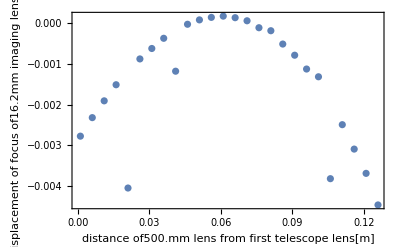

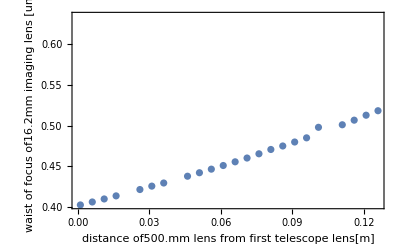

waist at min. displacement = 0.437854um

## save

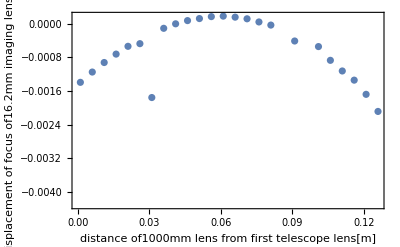

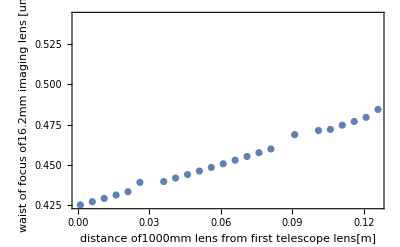

waist at min. displacement = 0.441868um

## save

```mathematica
{{0.020855172413793102,0.4175947091064325}}
```

```mathematica
{{0.008811188811188808,0.4287586703517507}}
```

# nominal focus position: 2960.63